```mathematica
(*Izračun števial Pi*)
Get[NotebookDirectory[]<>"mccPi.m"]


(*generacija poljubnega števila točk*)
t = Input["število točk:"];
{znKrog,točke}=mccPi[t];


(*calcPi*)
calcPi[{znKrog_,točke_}]:=Module[{približek,napaka},približek=4 *Length[znKrog]/Length[točke];
napaka=Abs[približek-Pi];
{približek,napaka}]
```

```mathematica
(*izračun približka in napake*)
{približek, napaka }= calcPi[{znKrog,točke}]
Print["približek za Pi:" ,približek,", ","napaka:", napaka ]
```

{396/125,396/125-π}

približek za Pi:396/125, napaka:396/125-π

```mathematica
(*grafučni prikaz rešitev*)
```

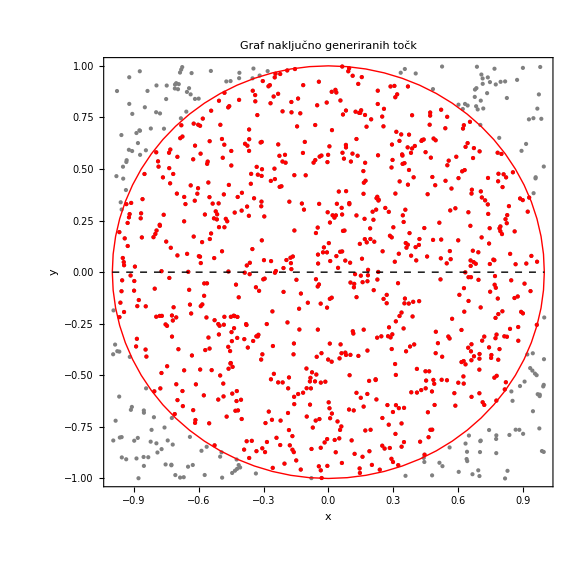

```mathematica
Graphics[{Gray,Point[točke],Red,Point[znKrog],Circle[{0,0},1,{0,2 Pi}],{Black,Dashed,Line[{{-1,0},{1,0}}]}},Frame->True,FrameLabel->{"x","y"},
ImageSize->Large,
PlotLabel->Style["Graf naključno generiranih točk",FontSize->18,Black],ImageSize->Medium,
FrameLabel->Style[{"x","y"}, FontSize->14,Black]]
```